## Define the coordinates and metric

### Sperical coordinates

```mathematica
coords$BL={t,y,r,ϑ,φ};
```

### Metric in Sperical coordinates

```mathematica
metric$BL=SymmetrizedArray[{
{1,1}-> -fS[r],
{2,2}->fB[r],
{3,3}->1/(fB[r]*fS[r]),
{4,4}->r^2,
{5,5}->r^2 Sin[ϑ]^2
},{5,5},Symmetric[{1,2}]]//Normal
```

{{-fS[r],0,0,0,0},{0,fB[r],0,0,0},{0,0,1/(fB[r] fS[r]),0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[ϑ]^2}}

```mathematica
MatrixForm[metric$BL]
```

(-fS[r] | 0 | 0 | 0 | 0
0 | fB[r] | 0 | 0 | 0
0 | 0 | 1/(fB[r] fS[r]) | 0 | 0
0 | 0 | 0 | r^2 | 0
0 | 0 | 0 | 0 | r^2 Sin[ϑ]^2)

### Inverse of metric

```mathematica
metric$BL$Inverse=Inverse[metric$BL]
```

{{-1/fS[r],0,0,0,0},{0,1/fB[r],0,0,0},{0,0,fB[r] fS[r],0,0},{0,0,0,1/r^2,0},{0,0,0,0,Csc[ϑ]^2/r^2}}

### Determinant

```mathematica
sqrtmg=Assuming[r>0&&Sin[ϑ]>0,√(-Det[metric$BL])//Simplify]
```

r^2 Sin[ϑ]

### Scalar equation

```mathematica
Operator$1=Table[sqrtmg*Sum[metric$BL$Inverse[[ac,bc]]*D[ψ[t,y,r,ϑ,φ],coords$BL[[bc]]],{bc,1,5}],{ac,1,5}]
```

{-(r^2 Sin[ϑ] ψ^(1,0,0,0,0)[t,y,r,ϑ,φ])/fS[r],(r^2 Sin[ϑ] ψ^(0,1,0,0,0)[t,y,r,ϑ,φ])/fB[r],r^2 fB[r] fS[r] Sin[ϑ] ψ^(0,0,1,0,0)[t,y,r,ϑ,φ],Sin[ϑ] ψ^(0,0,0,1,0)[t,y,r,ϑ,φ],Csc[ϑ] ψ^(0,0,0,0,1)[t,y,r,ϑ,φ]}

```mathematica
fB[r]=(1-rB/r);
fS[r]=(1-rS/r);
```

```mathematica
Eq$BL=1/sqrtmg Sum[D[Operator$1[[cc]],coords$BL[[cc]]],{cc,1,5}]//FullSimplify
```

ψ^(0,0,2,0,0)[t,y,r,ϑ,φ]+1/r^2(Csc[ϑ]^2 ψ^(0,0,0,0,2)[t,y,r,ϑ,φ]+Cot[ϑ] ψ^(0,0,0,1,0)[t,y,r,ϑ,φ]+ψ^(0,0,0,2,0)[t,y,r,ϑ,φ]+(2 r-rB-rS) ψ^(0,0,1,0,0)[t,y,r,ϑ,φ]-(-rB rS+r (rB+rS)) ψ^(0,0,2,0,0)[t,y,r,ϑ,φ]+r^3 ((ψ^(0,2,0,0,0)[t,y,r,ϑ,φ])/(r-rB)-(ψ^(2,0,0,0,0)[t,y,r,ϑ,φ])/(r-rS)))

```mathematica
(*/.{ψ_[t,y,r,ϑ,φ]->ψ}*)
```

```mathematica
fS[r]+fB[r]//Simplify
```

-(-2 r+rB+rS)/r

```mathematica
fS[r]fB[r]//FullSimplify
```

((r-rB) (r-rS))/r^2

### Reduce the scalar equation in the t, y direction

```mathematica
Scalar$Radial=Block[{ψ,ψr,res},
ψ[t_,y_,r_,ϑ_,φ_]:=Exp[-ⅈ*ω*t]*Exp[(ⅈ *n*y)/Ry]*ψY[ϑ,φ]*ψr[r];
res= Exp[ⅈ*ω*t]*Exp[-(ⅈ *n*y)/Ry]/ψY[ϑ,φ]*Expand[Eq$BL]
]//FullSimplify
```

((2 r-rB-rS) ψr'[r]+(r-rB) (r-rS) ψr''[r]+ψr[r] (r^3 (-n^2/((r-rB) Ry^2)+ω^2/(r-rS))+(Csc[ϑ]^2 ψY^(0,2)[ϑ,φ]+Cot[ϑ] ψY^(1,0)[ϑ,φ]+ψY^(2,0)[ϑ,φ])/ψY[ϑ,φ]))/r^2

## Define the Φ Function

```mathematica
Phi[l_,m_,ωs_,rb_,r_,θo_,ϕo_,μ_,q_,rB_,rS_,Ry_]:=Module[
{M,d,rs,θs,R,S,ϵS,ϵB,wronskian,ω,θ,kS,α,β,Ain,B,Ψm,Ψp,Ψmmin,Ψpmax,RadialFunction,ut,fB,$RecursionLimit=Infinity},

M=1;(*unit*)
ω=m*ωs;(*frequency of GW*)
d=1/2 ((2 μ)/ωs^2)^(1/3)(*radius of binary orbit*);
rs=√(rb^2+d^2);
θs=ArcCos[-rb/Sqrt[rb^2+d^2]];
ut=1/(√(1-rS/rs-ωs^2*rs^2*Sin[θs]^2));
fB=1-rB/rs;
ϵS=ω*rS;
ϵB=ω*rB;
kS=√(rS^3/(rS-rB));
α=If[rS>=rB,
-I*kS*ω,
0];
β=If[rS>=rB,
1/2(1-√((1+2l)^2+4 α^2)),
1/2(1-√((1+2l)^2+4(rB^3*ω^2)/(rB-rS)))]; 
Ain=If[rS>=rB,
(I^(l+1)(2*rS)^(l+1)Gamma[l+3/2]Gamma[1+2α]Gamma[1-2β])/(2 √π ϵS^(l+1)rS^(3/4)(rS-rB)^(l+1/4)Gamma[1+α-β]^2),
(I^(l+1)(2*rS)^(l+1)Gamma[l+3/2]Gamma[-2β])/(2 √π ϵS^(l+1)rB^(3/4)(rB-rS)^l Gamma[1-β]^2)];

B=If[rS>=rB,
((2rS)^(l+1)Gamma[l+3/2]Gamma[1+2α]Gamma[1-2β])/(√2 ϵS^(l+1)rS^(3/4)(rS-rB)^(l+1/4)Gamma[1+α-β]^2),
((2rS)^(l+1)Gamma[l+3/2]Gamma[-2β])/(√2 ϵS^(l+1)rB^(3/4)(rB-rS)^l Gamma[1-β]^2)];
Ψm[rvar_]:=(B √2 ϵS^(l+1))/((2rS)^(l+1)Gamma[l+3/2])rvar^(l+1);
Ψp[rvar_]:=I^l(2^l ω^-l)/(√π)Gamma[l+1/2] rvar^-l;
wronskian=2*I*ω*Ain;   
Ψmmin=Ψm[Min[rs,r]];  
Ψpmax=Ψp[Max[rs,r]]; 

RadialFunction=If[rs<=r,
Ψpmax/wronskian*(2*μ*q)/(ut*Ry)*Ψmmin/(rs*fB^(1/4))*Conjugate[SphericalHarmonicY[l,m,θs,0]],
Ψmmin/wronskian*(2*μ*q)/(ut*Ry)*Ψpmax/(rs*fB^(1/4))*Conjugate[SphericalHarmonicY[l,m,θs,0]]];
1/(2π)1/r 1/(1-rB/r)^(1/4)*RadialFunction*SphericalHarmonicY[l,m,θo,ϕo]
]
```

```mathematica
α=-I*kS*ω;
Series[(Gamma[1+2α]Gamma[1-2β])/Gamma[1+α-β]^2,{ω,0,0}]//Simplify
```

```mathematica
Gamma[1-2 β]/Gamma[1-β]^2+O[ω]^1
```

Gamma[1-2 β]/Gamma[1-β]^2+O[ω]^1

## Psi4-thetao curve for BHs

### DiscretePlot3D of Φ

```mathematica
Phil[l_,θoplot_,rB_,rS_]:=N[Norm[Phi[l,2,SetPrecision[0.01,130],10,20,θoplot,0,SetPrecision[10^-4,130],SetPrecision[10^-4,130],rB,rS,0.01]]]
```

```mathematica
(*DiscretePlot3D of Φ for l：l∈[2,100]，θoplot∈[0,π]，rB=3.8，rS=2*)
Phi3Dl=DiscretePlot3D[Phil[l,θoplot,3,2],{l,2,20,1},{θoplot,0,π,π/20},AxesLabel->{"l",ToExpression["$\\theta_o$",TeXForm],ToExpression["$|\\Phi|$",TeXForm]},ColorFunction->"Rainbow",ImageSize->Large]
```

-Graphics3D-

```mathematica
Export["C:\\Users\\zzq\\Desktop\\Paolo Pani\\Topological star\\拓扑星Lensing\\final\\Phi3D-l.pdf",Phi3Dl,"PDF"]
```

C:\Users\zzq\Desktop\Paolo Pani\Topological star\拓扑星Lensing\final\Phi3D-l.pdf

```mathematica
Phim[m_,θoplot_,rB_,rS_]:=N[Norm[ParallelSum[Phi[l,m,0.01,10,20,θoplot,0,0.01,0.01,rB,rS,0.01],{l,m,20}]]]
```

```mathematica
(*DiscretePlot3D of Φ for m：l∈[2,20]，θoplot∈[0,π]，rB=3.8，rS=2*)
Phi3Dm=DiscretePlot3D[Phim[m,θoplot,3,2],{m,2,10,2},{θoplot,0,π,π/20},AxesLabel->{"m",ToExpression["$\\theta_o$",TeXForm],ToExpression["$|\\Phi|$",TeXForm]},ColorFunction->"Rainbow",ImageSize->Large]
```

-Graphics3D-

```mathematica
Export["C:\\Users\\zzq\\Desktop\\Paolo Pani\\Topological star\\拓扑星Lensing\\final\\Phi3D-m.pdf",Phi3Dm,"PDF"]
```

C:\Users\zzq\Desktop\Paolo Pani\Topological star\拓扑星Lensing\final\Phi3D-m.pdf

### observer far away from the source

```mathematica
(*l_,m_,ωs_,rs_,r_,θo_,ϕo_,μ_,q_,rB_,rS_,Ry_,n_,y_*)
```

```mathematica
PhithetaoPlot$far[m_,θoplot_,rB_,rS_]:=N[Norm[ParallelSum[Phi[l,m,0.01,10,20,θoplot,0,10^-4,10^-4,rB,rS,0.01],{l,2,20}]]]
```

```mathematica
thetapoints:=Table[t,{t,0,π,π/100}]
```

```mathematica
Phimodevalues$far={Table[PhithetaoPlot$far[2,t,0,2],{t,thetapoints}],Table[PhithetaoPlot$far[2,t,2*0.5,2],{t,thetapoints}],Table[PhithetaoPlot$far[2,t,2*0.99,2],{t,thetapoints}],Table[PhithetaoPlot$far[2,t,2*1.1,2],{t,thetapoints}],Table[PhithetaoPlot$far[2,t,2*1.5,2],{t,thetapoints}],Table[PhithetaoPlot$far[2,t,2*1.9,2],{t,thetapoints}]};
```

```mathematica
xticks:=Range[0,π,π/8]
```

```mathematica
yticks:=Range[0,1.5*^-12,1.5*^-12/5]
```

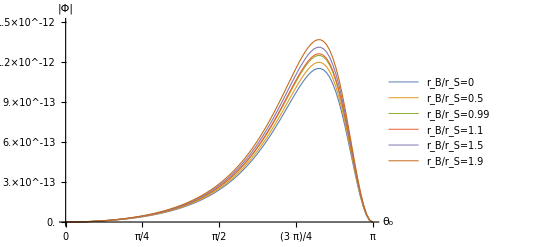

```mathematica
Phithetao$far=ListLinePlot[{Transpose[{thetapoints,Phimodevalues$far[[1]]}],Transpose[{thetapoints,Phimodevalues$far[[2]]}],Transpose[{thetapoints,Phimodevalues$far[[3]]}],Transpose[{thetapoints,Phimodevalues$far[[4]]}],Transpose[{thetapoints,Phimodevalues$far[[5]]}],Transpose[{thetapoints,Phimodevalues$far[[6]]}]},Ticks->{xticks,yticks},PlotRange->{{0,π},{0,1.5*^-12}},GridLines->{Range[0,π,π/8],Range[0,1.5*^-12,1.5*^-12/5]},PlotStyle->{Thickness[0.002]},PlotLegends->{"r_B/r_S=0","r_B/r_S=0.5","r_B/r_S=0.99","r_B/r_S=1.1","r_B/r_S=1.5","r_B/r_S=1.9"},AxesLabel->{"θ_o","|Φ|"}]
```

```mathematica
Export["C:\\Users\\zzq\\Desktop\\Paolo Pani\\Topological star\\拓扑星Lensing\\final\\Phithetaofar.pdf",Phithetao$far,"PDF"]
```

C:\Users\zzq\Desktop\Paolo Pani\Topological star\拓扑星Lensing\final\Phithetaofar.pdf

#### Density plot of Re[Φ]

```mathematica
(*l_,m_,ωs_,rs_,r_,θo_,ϕo_,μ_,q_,rB_,rS_,Ry_*)
```

#### BH

```mathematica
PhiReDensityPlot[θoplot_,roplot_]:=

Re[ParallelSum[Phi[l,-2,0.01,100,roplot,θoplot,0,10^-4,10^-4,1,2,0.01],{l,2,20}]]+Re[ParallelSum[Phi[l,2,0.01,100,roplot,θoplot,0,10^-4,10^-4,1,2,0.01],{l,2,20}]]
```

```mathematica
(*data=Table[With[{roplot=RandomReal[{11,60}],θoplot=RandomReal[{0,2π}]},{roplot*Sin[θoplot],roplot*Cos[θoplot],Psi4ReDensityPlot[θoplot,roplot]}],20000]*)
```

```mathematica
dataxBH:=Table[roplot*Cos[θoplot],{roplot,2,60,2},{θoplot,0,2π,2π/60}]
datayBH:=Table[roplot*Sin[θoplot],{roplot,2,60,2},{θoplot,0,2π,2π/60}]
dataPhi:=Table[PhiReDensityPlot[θoplot,roplot],{roplot,2,60,2},{θoplot,0,2π,2π/60}]
```

```mathematica
dataBH=Transpose[{Flatten[datayBH],Flatten[dataxBH],Flatten[dataPhi]}]
```

```mathematica
dataBHExport=dataBH//N;
```

```mathematica
(* Export dataBH to CSV form*)
Export["C:\\Users\\zzq\\Desktop\\Paolo Pani\\Topological star\\拓扑星Lensing\\final\\BH_data.csv", dataBHExport, "CSV"];
```

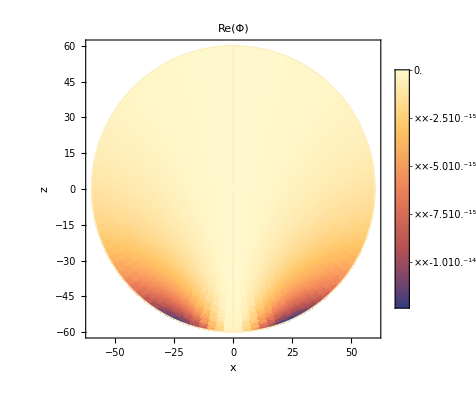

```mathematica
Density$BH=ListDensityPlot[dataBH,PlotRange->{{-60,60},{-60,60},{-9^-20,-0.1}},Axes->True,AxesLabel->{x,z},PlotLabel->Style["Re(Φ)",Black],PlotLegends->Automatic,BoundaryStyle->Red,InterpolationOrder->1]
```

```mathematica
Export["C:\\Users\\zzq\\Desktop\\Paolo Pani\\Topological star\\拓扑星Lensing\\Density$BH.pdf",Density$BH,"PDF"]
```

C:\Users\zzq\Desktop\Paolo Pani\Topological star\拓扑星Lensing\Density$BH.pdf

#### TS

```mathematica
PhiReDensityPlot$TS[θoplot_,roplot_]:=

Re[ParallelSum[Phi[l,-2,0.01,100,roplot,θoplot,0,10^-4,10^-4,2,1,0.01],{l,2,20}]]+Re[ParallelSum[Phi[l,2,0.01,100,roplot,θoplot,0,10^-4,10^-4,2,1,0.01],{l,2,20}]]
```

```mathematica
(*data=Table[With[{roplot=RandomReal[{11,60}],θoplot=RandomReal[{0,2π}]},{roplot*Sin[θoplot],roplot*Cos[θoplot],Psi4ReDensityPlot[θoplot,roplot]}],20000]*)
```

```mathematica
dataxTS:=Table[roplot*Cos[θoplot],{roplot,2,60,2},{θoplot,0,2π,2π/60}]
datayTS:=Table[roplot*Sin[θoplot],{roplot,2,60,2},{θoplot,0,2π,2π/60}]
```

```mathematica
dataPhi$TS:=Table[PhiReDensityPlot$TS[θoplot,roplot],{roplot,2,60,2},{θoplot,0,2π,2π/60}]
```

```mathematica
data$TS=Transpose[{Flatten[datayTS],Flatten[dataxTS],Flatten[dataPhi$TS]}];
```

```mathematica
Density$TS=ListDensityPlot[data$TS,PlotRange->{{-60,60},{-60,60},{-9^-20,-0.1}},Axes->True,AxesLabel->{x,z},PlotLabel->Style["Re(Φ)",Black],PlotLegends->Automatic,BoundaryStyle->Red,InterpolationOrder->1]
```

```mathematica
Export["C:\\Users\\zzq\\Desktop\\Paolo Pani\\Topological star\\拓扑星Lensing\\Density$TS.pdf",Density$TS,"PDF"]
```

C:\Users\zzq\Desktop\Paolo Pani\Topological star\拓扑星Lensing\Density$BH.pdf